```mathematica
Quit[]
```

## USR2SR

```mathematica
$Assumptions={ϵ0>0,τ<0,τ0<0,H>0,k>0,p>0,xe>0};
```

```mathematica
ζk[τ_,k_]=H/Sqrt[4ϵ0 k^3](τ0/τ)^3(1+I k τ)E^(-I k τ);
```

```mathematica
ζks[τ_,k_]=Conjugate[ζk[τ,k]]//FullSimplify
```

(ⅇ^(ⅈ k τ) H (1-ⅈ k τ) τ0^3)/(2 √(k^3 ϵ0) τ^3)

```mathematica
Pk[τ_,k_]=ζks[τ,k]ζk[τ,k]//Simplify
```

(H^2 (1+k^2 τ^2) τ0^6)/(4 k^3 ϵ0 τ^6)

```mathematica
PUSR[x_,k_]=Normal[Series[Pk[x τ0,k],{x,0,-6}]]//ExpToTrig//FullSimplify
```

H^2/(4 k^3 x^6 ϵ0)

```mathematica
pktk[τ_,τp_,p_,k_]=ζk[τ,p]ζk[τ,k]ζk[τ,k]ζks[τp,p]ζks[τp,k]D[ζks[τp,k], τp]//Simplify
```

(ⅇ^(-ⅈ (2 k+p) (τ-τp)) H^6 (-ⅈ+k τ)^2 (1+ⅈ p τ) τ0^18 (ⅈ+k τp) (ⅈ+p τp) (-3+3 ⅈ k τp+k^2 τp^2))/(64 k^6 p^3 ϵ0^3 τ^9 τp^10)

```mathematica
pktkim[xe_,p_,k_]=Normal[Series[pktk[xe τ0,xe τ0,p,k],{xe,0,-16}]]//ExpToTrig//Simplify//Im//Simplify
```

(H^6 τ0^2)/(64 k^3 p^3 xe^16 ϵ0^3)

```mathematica
Normal[Series[5/12(2/(xe^2 τ0^2 H^2)xe^6 ϵ0 Δηe pktkim[xe,p,k]2)/(PUSR[xe,p]PUSR[xe,k]),{xe,0,0}]]
```

(5 Δηe)/12

```mathematica
kktp[τ_,τp_,p_,k_]=ζk[τ,k]ζk[τ,k]ζk[τ,p]ζks[τp,k]ζks[τp,k]D[ζks[τp,p], τp]//Simplify
```

(ⅇ^(-ⅈ (2 k+p) (τ-τp)) H^6 (-ⅈ+k τ)^2 (1+ⅈ p τ) τ0^18 (ⅈ+k τp)^2 (-3+3 ⅈ p τp+p^2 τp^2))/(64 k^6 p^3 ϵ0^3 τ^9 τp^10)

```mathematica
kktpim[xe_,p_,k_]=Normal[Series[kktp[xe τ0,xe τ0,p,k],{xe,0,-16}]]//ExpToTrig//Simplify//Im//Simplify
```

(H^6 τ0^2)/(64 k^6 xe^16 ϵ0^3)

## SR2USR2SR sharp

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,H>0,k>0,p>0,xe>0};
```

```mathematica
Ak[k_]=1-(3(1+k^2 τs^2))/(2I k^3 τs^3);
Bk[k_]=-(3(1+I k τs)^2)/(2I k^3 τs^3)Exp[-2I k τs];
ζk[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τ)^3 1/k^(3/2)(Ak[k] E^(-I k τ)(1+I k τ)-Bk[k] E^(I k τ)(1-I k τ));
```

```mathematica
ζks[τ_,k_]=Conjugate[ζk[τ,k]]//FullSimplify
```

-(ⅈ H (3 ⅇ^(-ⅈ k (τ-2 τs)) (-ⅈ+k τ) (ⅈ+k τs)^2+ⅇ^(ⅈ k τ) (1-ⅈ k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(4 √(k^9 ϵSR) τ^3)

```mathematica
Pk[τ_,k_]=ζks[τ,k]ζk[τ,k]//Simplify
```

1/(16 k^9 ϵSR τ^6)H^2 (3 ⅇ^(ⅈ k (τ-2 τs)) (ⅈ+k τ) (-ⅈ+k τs)^2+ⅇ^(-ⅈ k τ) (1+ⅈ k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)) (3 ⅇ^(-ⅈ k (τ-2 τs)) (-ⅈ+k τ) (ⅈ+k τs)^2+ⅇ^(ⅈ k τ) (1-ⅈ k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs)))

```mathematica
PSR[p_]=Normal[Series[Pk[τ,p],{p,0,-3}]]
```

H^2/(4 p^3 ϵSR)

```mathematica
PUSR[x_,k_]=Normal[Series[Pk[x τs,k],{x,0,-6}]]//ExpToTrig//FullSimplify
```

(H^2 (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6+3 (-3+7 k^4 τs^4) Cos[2 k τs]+6 k τs (-3-4 k^2 τs^2+k^4 τs^4) Sin[2 k τs]))/(8 k^9 x^6 ϵSR τs^6)

```mathematica
calPk[τ_,k_]=k^3/(2 π^2)Pk[τ,k];
```

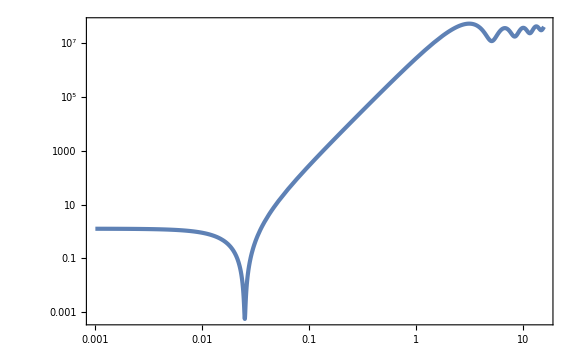

```mathematica
LogLogPlot[calPk[-10^-1.2,k]/.{ϵSR->10^-2,H->1,τs->-1},{k,10^-3,10^1.2}]
```

```mathematica
nsm1[τ_,k_]=k D[Log[calPk[τ,k]], k]//Simplify;
```

```mathematica
nsm1e[k_]=Normal[Series[nsm1[xe τs,k],{xe,0,0}]]//Simplify
```

(6 (9+18 ⅈ k τs-6 k^2 τs^2+12 ⅈ k^3 τs^3-15 k^4 τs^4-8 ⅈ k^5 τs^5+2 k^6 τs^6-6 ⅇ^(2 ⅈ k τs) (3+4 k^2 τs^2+k^4 τs^4)+ⅇ^(4 ⅈ k τs) (9-18 ⅈ k τs-6 k^2 τs^2-12 ⅈ k^3 τs^3-15 k^4 τs^4+8 ⅈ k^5 τs^5+2 k^6 τs^6)))/((3+3 k^2 τs^2+2 ⅈ k^3 τs^3+3 ⅇ^(2 ⅈ k τs) (ⅈ+k τs)^2) (3 (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (3+3 k^2 τs^2-2 ⅈ k^3 τs^3)))

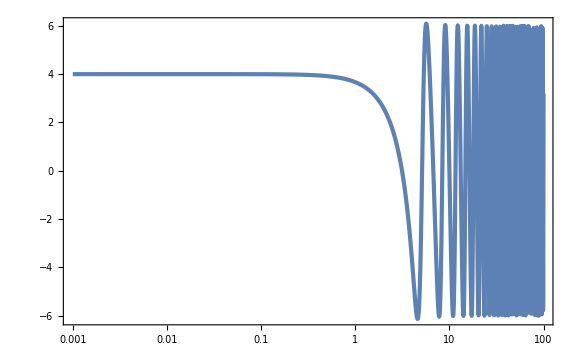

```mathematica
LogLinearPlot[nsm1e[k]/.{τs->-1},{k,10^-3,10^2},WorkingPrecision->30]
```

```mathematica
pktk[τ_,τp_,p_,k_]=ζk[τ,p]ζk[τ,k]ζk[τ,k]ζks[τp,p]ζks[τp,k]D[ζks[τp,k], τp]//Simplify
```

1/(4096 k^18 p^9 ϵSR^3 τ^9 τp^10)ⅇ^(-ⅈ (2 k+p) (τ+τp)) H^6 (3 (1+ⅈ k τp) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (ⅈ+k τp) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (-3 ⅈ (-3-3 ⅈ k τp+k^2 τp^2) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (-3+3 ⅈ k τp+k^2 τp^2) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (3 ⅇ^(2 ⅈ k τ) (1-ⅈ k τ) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3))^2 (-3 (-ⅈ+p τp) (ⅈ+p τs)^2+ⅇ^(2 ⅈ p (τp-τs)) (ⅈ+p τp) (3+3 p^2 τs^2+2 ⅈ p^3 τs^3)) (3 ⅇ^(2 ⅈ p τ) (1-ⅈ p τ) (-ⅈ+p τs)^2+ⅇ^(2 ⅈ p τs) (-ⅈ+p τ) (3 ⅈ+3 ⅈ p^2 τs^2+2 p^3 τs^3))

```mathematica
pktkeim[xe_,p_,k_]=Normal[Series[pktk[xe τs,xe τs,p,k],{p,0,-3},{xe,0,-6}]]//ExpToTrig//Simplify//Im//Simplify
```

1/(128 k^9 p^3 xe^10 ϵSR^3 τs^4)H^6 ((1+k^2 xe^2 τs^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6)+(-9-9 k^2 xe^2 τs^2+3 k^4 (7+4 xe^3) τs^4+k^6 xe^2 (21+16 xe) τs^6-4 k^8 xe^3 τs^8) Cos[2 k τs]+2 k τs (-9-3 k^2 (4+3 xe^2+xe^3) τs^2+3 k^4 (1-4 xe^2) τs^4+k^6 xe^2 (3+7 xe) τs^6) Sin[2 k τs])

```mathematica
Normal[Series[5/12(2/(xe^2 τs^2 H^2)xe^6 ϵSR Δηe pktkeim[xe,p,k]2)/(PSR[p]PUSR[xe,k]),{xe,0,0}]]
```

(5 Δηe)/12

```mathematica
pktksim[xe_,p_,k_]=Normal[Series[pktk[xe τs,τs,p,k],{p,0,-3},{xe,0,-6}]]//ExpToTrig//Expand//Im//FullSimplify
```

1/(128 k^9 p^3 xe^6 ϵSR^3 τs^4)H^6 (3 (3+4 k^2 τs^2+k^4 τs^4)+(-9+6 k^2 τs^2+15 k^4 τs^4-2 k^6 τs^6) Cos[2 k τs]+2 k τs (-9-6 k^2 τs^2+4 k^4 τs^4) Sin[2 k τs])

```mathematica
fNLpktks[x_]=Normal[Series[5/12(2/(τs^2 H^2)ϵSR Δηe pktksim[xe,p,k]2)/(PSR[p]PUSR[xe,k]),{xe,0,0}]]/.{k->x/τs}//Simplify
```

(5 Δηe (3 (3+4 x^2+x^4)+(-9+6 x^2+15 x^4-2 x^6) Cos[2 x]+2 x (-9-6 x^2+4 x^4) Sin[2 x]))/(12 (9+18 x^2+9 x^4+2 x^6+3 (-3+7 x^4) Cos[2 x]+6 x (-3-4 x^2+x^4) Sin[2 x]))

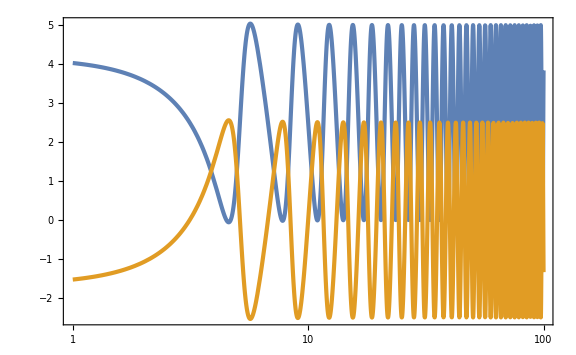

```mathematica
LogLinearPlot[{fNLpktks[x]+5/2/.{Δηe->-6},-5/12 nsm1e[x]/.{τs->-1}},{x,10^0,10^2},WorkingPrecision->30]
```

```mathematica
kktp[τ_,τp_,p_,k_]=ζk[τ,p]ζk[τ,k]ζk[τ,k]ζks[τp,k]ζks[τp,k]D[ζks[τp,p], τp]//Simplify
```

1/(4096 k^18 p^9 ϵSR^3 τ^9 τp^10)ⅇ^(-ⅈ (2 k+p) (τ+τp)) H^6 (3 (1+ⅈ k τp) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (ⅈ+k τp) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3))^2 (3 ⅇ^(2 ⅈ k τ) (1-ⅈ k τ) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3))^2 (3 (-3-3 ⅈ p τp+p^2 τp^2) (ⅈ+p τs)^2+ⅇ^(2 ⅈ p (τp-τs)) (-3+3 ⅈ p τp+p^2 τp^2) (3+3 p^2 τs^2+2 ⅈ p^3 τs^3)) (3 ⅇ^(2 ⅈ p τ) (1-ⅈ p τ) (-ⅈ+p τs)^2+ⅇ^(2 ⅈ p τs) (-ⅈ+p τ) (3 ⅈ+3 ⅈ p^2 τs^2+2 p^3 τs^3))

```mathematica
kktpeim[xe_,p_,k_]=Normal[Series[kktp[xe τs,xe τs,p,k],{p,0,-3},{x,0,-6}]]//ExpToTrig//Simplify//Im//Simplify
```

0

```mathematica
kktpsim[xe_,p_,k_]=Normal[Series[kktp[xe τs,τs,p,k],{p,0,-3},{x,0,-6}]]//ExpToTrig//Simplify//Im//Simplify
```

0

## SR2USR2SR sharp specific value

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,H>0,k>0,p>0,xe>0};
```

```mathematica
Ak[k_]=1-(3(1+k^2 τs^2))/(2I k^3 τs^3);
Bk[k_]=-(3(1+I k τs)^2)/(2I k^3 τs^3)Exp[-2I k τs];
ζk[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τ)^3 1/k^(3/2)(Ak[k] E^(-I k τ)(1+I k τ)-Bk[k] E^(I k τ)(1-I k τ));
```

```mathematica
ζks[τ_,k_]=Conjugate[ζk[τ,k]]//FullSimplify
```

-(ⅈ H (3 ⅇ^(-ⅈ k (τ-2 τs)) (-ⅈ+k τ) (ⅈ+k τs)^2+ⅇ^(ⅈ k τ) (1-ⅈ k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(4 √(k^9 ϵSR) τ^3)

```mathematica
Pk[τ_,k_]=ζks[τ,k]ζk[τ,k]//ExpToTrig//Expand//Simplify
```

1/(8 k^9 ϵSR τ^6)H^2 ((1+k^2 τ^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6)-3 (3-3 k^2 τ (τ-4 τs)+k^4 (16 τ-7 τs) τs^3+k^6 τ (7 τ-4 τs) τs^4) Cos[2 k (τ-τs)]+6 k (3 τs+4 k^2 τs^3-k^4 τs^5+k^2 τ^2 τs (-3-4 k^2 τs^2+k^4 τs^4)+τ (-3+7 k^4 τs^4)) Sin[2 k (τ-τs)])

```mathematica
calPk[τ_,k_]=k^3/(2 π^2)Pk[τ,k];
```

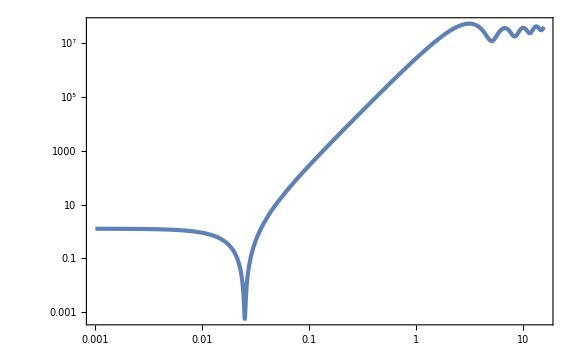

```mathematica
LogLogPlot[calPk[-10^(-12/10),k]/.{ϵSR->10^-2,H->1,τs->-1},{k,10^-3,10^(12/10)},WorkingPrecision->30]
```

```mathematica
nsm1[τ_,k_]=k D[Log[calPk[τ,k]], k]//Simplify;
```

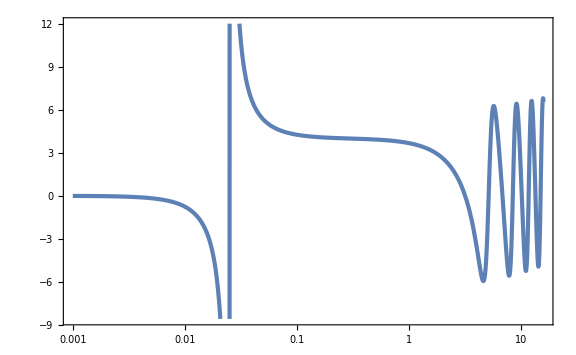

```mathematica
LogLinearPlot[nsm1[-10^(-12/10),k]/.{τs->-1},{k,10^-3,10^(12/10)},WorkingPrecision->30]
```

```mathematica
pktk[τ_,τp_,p_,k_]=ζk[τ,p]ζk[τ,k]ζk[τ,k]ζks[τp,p]ζks[τp,k]D[ζks[τp,k], τp]//Simplify
```

1/(4096 k^18 p^9 ϵSR^3 τ^9 τp^10)ⅇ^(-ⅈ (2 k+p) (τ+τp)) H^6 (3 (1+ⅈ k τp) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (ⅈ+k τp) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (-3 ⅈ (-3-3 ⅈ k τp+k^2 τp^2) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (-3+3 ⅈ k τp+k^2 τp^2) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (3 ⅇ^(2 ⅈ k τ) (1-ⅈ k τ) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3))^2 (-3 (-ⅈ+p τp) (ⅈ+p τs)^2+ⅇ^(2 ⅈ p (τp-τs)) (ⅈ+p τp) (3+3 p^2 τs^2+2 ⅈ p^3 τs^3)) (3 ⅇ^(2 ⅈ p τ) (1-ⅈ p τ) (-ⅈ+p τs)^2+ⅇ^(2 ⅈ p τs) (-ⅈ+p τ) (3 ⅈ+3 ⅈ p^2 τs^2+2 p^3 τs^3))

```mathematica
fNLe[p_,k_]=5/3 1/(xe^2 τs^2 H^2)(xe^6 ϵSR Δηe Im[pktk[xe τs,xe τs,p,k]])/(Pk[xe τs,p]Pk[xe τs,k]);
```

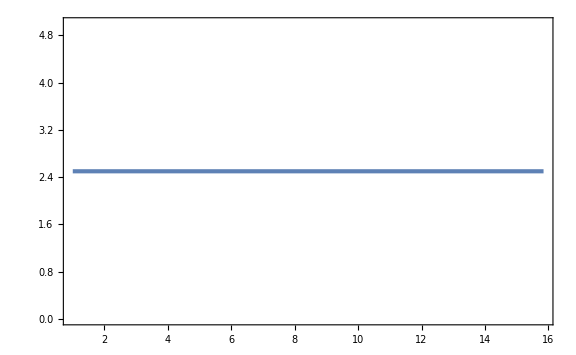

```mathematica
Plot[fNLe[10^-3,k]/.{xe->10^(-12/10),τs->-1,H->1,ϵSR->10^-2,Δηe->6},{k,1,10^(12/10)},WorkingPrecision->30]
```

```mathematica
fNLs[p_,k_]=-5/3 1/(τs^2 H^2)(ϵSR Δηe Im[pktk[xe τs,τs,p,k]])/(Pk[xe τs,p]Pk[xe τs,k]);
```

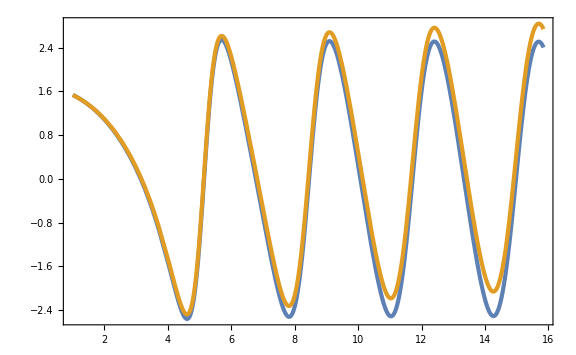

```mathematica
Plot[{fNLs[10^-3,k]/.{xe->10^(-12/10),τs->-1,H->1,ϵSR->10^-2,Δηe->6},5/12 nsm1[-10^(-12/10),k]/.{τs->-1}},{k,1,10^(12/10)},WorkingPrecision->30]
```

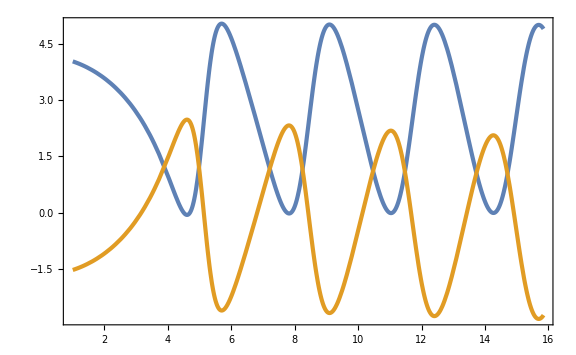

```mathematica
Plot[{fNLe[10^-3,k]+fNLs[10^-3,k]/.{xe->10^(-12/10),τs->-1,H->1,ϵSR->10^-2,Δηe->6},-5/12 nsm1[-10^(-12/10),k]/.{τs->-1}},{k,1,10^(12/10)},WorkingPrecision->30]
```

## SR2USR

```mathematica
$Assumptions={ϵ0>0,τ0<0,τs<0,τ<0};
```

```mathematica
η[τ_]=-6 (1-Tanh[Log[τ/τs]/(5 10^-2)])/2//Simplify
```

3 (-1+Tanh[20 Log[τ/τs]])

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)];lndt//N
```

1.1165

```mathematica
Log10[(10^-2/(2 10^-9))^(1/4)]//N
```

1.67474

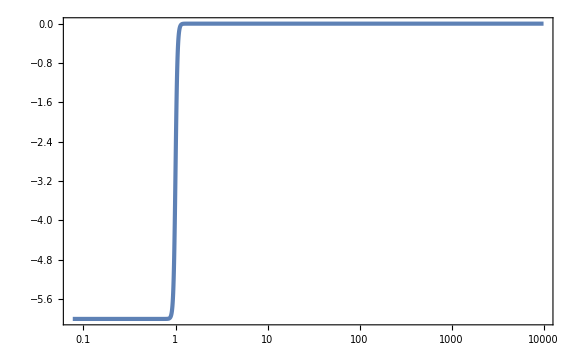

```mathematica
LogLinearPlot[η[-x]/.{τs->-1},{x,10^-lndt,10^4}]
```

```mathematica
ηint[τ_]=Integrate[-η[τ]/τ,τ]//Simplify
```

6 Log[τ]-3/20 Log[τ^40+τs^40]

```mathematica
ϵ[τ_]=ϵ0 Exp[ηint[τ]-ηint[τ0]]//Simplify
```

(ϵ0 τ^6 ((τ0^40+τs^40)/(τ^40+τs^40))^(3/20))/τ0^6

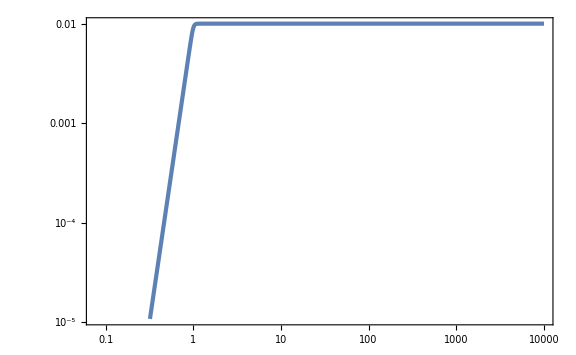

```mathematica
LogLogPlot[ϵ[-x]/.{τs->-1,τ0->-10^4,ϵ0->10^-2},{x,10^-lndt,10^4}]
```

```mathematica
z[τ_]=-1/(τ H)Sqrt[2ϵ[τ]]/.{H->1}//Simplify
```

-(√2 √ϵ0 τ^2 ((τ0^40+τs^40)/(τ^40+τs^40))^(3/40))/τ0^3

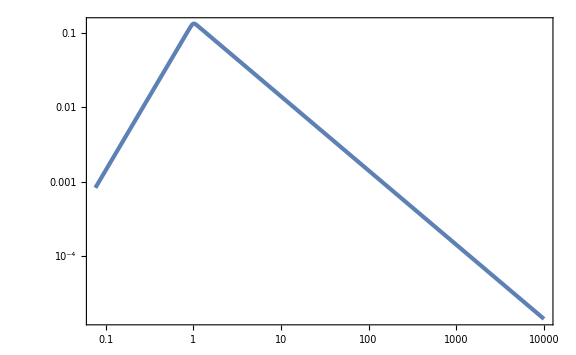

```mathematica
LogLogPlot[z[-x]/.{τs->-1,τ0->-10^4,ϵ0->10^-2},{x,10^-lndt,10^4}]
```

```mathematica
EoM=vk''[τ]+(k^2-z''[τ]/z[τ])vk[τ]==0//Simplify
```

((-2 τ^80+k^2 τ^82+125 τ^40 τs^40+2 k^2 τ^42 τs^40-2 τs^80+k^2 τ^2 τs^80) vk[τ])/(τ^2 (τ^40+τs^40)^2)+vk''[τ]==0

```mathematica
kL=3 10^-3;
kS=8.5;
vkL[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τs->-1,τ0->-10^4,k->kL},vk[τ],{τ,-10^4,-10^-lndt}(*,WorkingPrecision->30,MaxSteps->10^6*)][[1]];//AbsoluteTiming
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τs->-1,τ0->-10,k->kS},vk[τ],{τ,-10,-10^-lndt}(*,WorkingPrecision->20,MaxSteps->10^5*)][[1]];//AbsoluteTiming
```

{0.006995,Null}

{0.003034,Null}

```mathematica
ζkL[τ_]=vkL[τ]/z[τ]/.{τs->-1,τ0->-10^4,ϵ0->10^-2};
ζkS[τ_]=vkS[τ]/z[τ]/.{τs->-1,τ0->-10,ϵ0->10^-2};
PζkL[τ_]=Norm[ζkL[τ]]^2;
PζkS[τ_]=Norm[ζkS[τ]]^2;
```

```mathematica
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
```

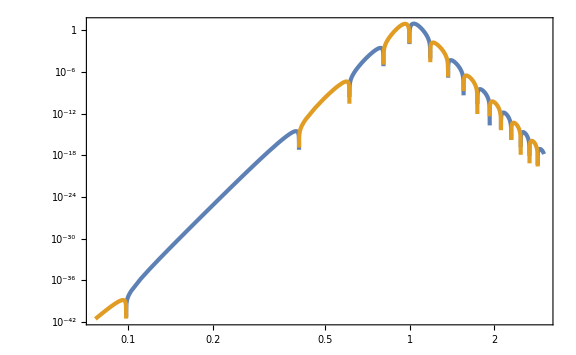

```mathematica
LogLogPlot[{5/12 1/(PζkL[-10^-lndt]PζkS[-10^-lndt])2Im[2/τp^2(ϵ[-τp]η'[-τp]/.{τs->-1,τ0->-10^4,ϵ0->10^-2})pktk[-10^-lndt,-τp]],-5/12 1/(PζkL[-10^-lndt]PζkS[-10^-lndt])2Im[2/τp^2(ϵ[-τp]η'[-τp]/.{τs->-1,τ0->-10^4,ϵ0->10^-2})pktk[-10^-lndt,-τp]]},{τp,10^-lndt,3}]
```

```mathematica
5/12 1/(PζkL[-10^-lndt]PζkS[-10^-lndt])2NIntegrate[Im[2/τp^2(ϵ[τp]η'[τp]/.{τs->-1,τ0->-10^4,ϵ0->10^-2})pktk[-10^-lndt,τp]],{τp,-10,-10^-lndt}]
```

0.0775123

## SR2USR2SR num

```mathematica
$Assumptions={ϵ0>0,τ0<0,τs<0,τ<0,lnDt>0};
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)];lndt//N
```

1.1165

```mathematica
η[τ_]=-6 (1-Tanh[Log[τ/τs]/(5 10^-2)])/2(1-Tanh[Log[(τs 10^-lnDt)/τ]/(5 10^-2)])/2//FullSimplify
```

-3/2 (-1+Tanh[20 Log[τ/τs]]) (-1+Tanh[20 Log[(10^-lnDt τs)/τ]])

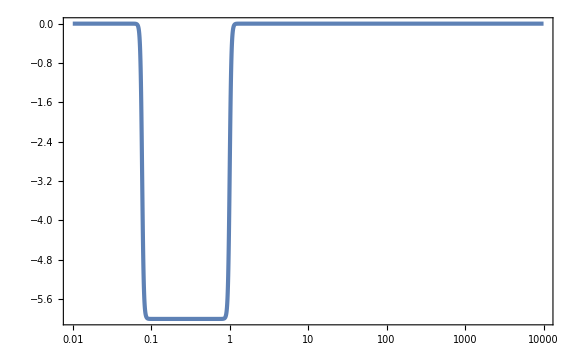

```mathematica
LogLinearPlot[η[-x]/.{τs->-1,lnDt->lndt},{x,10^-2,10^4},PlotRange->Full]
```

```mathematica
ηint[τ_]=Integrate[-η[τ]/τ,τ]//Simplify
```

-3/40 (1+Coth[20 lnDt Log[10]]) Log[(10^(20 lnDt) (τ^40+τs^40))/(10^(40 lnDt) τ^40+τs^40)]

```mathematica
ϵ[τ_]=ϵ0 Exp[ηint[τ]-ηint[τ0]]//Simplify
```

ϵ0 (((τ^40+τs^40) (10^(40 lnDt) τ0^40+τs^40))/((10^(40 lnDt) τ^40+τs^40) (τ0^40+τs^40)))^(-3/40 (1+Coth[20 lnDt Log[10]]))

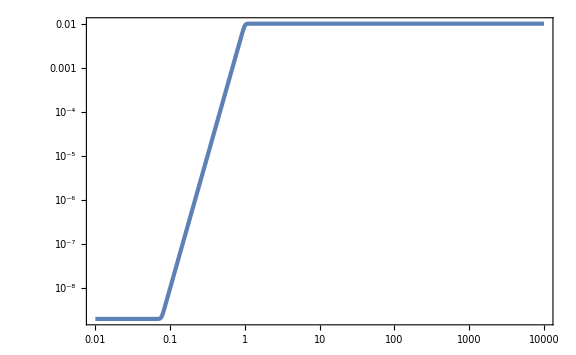

```mathematica
LogLogPlot[ϵ[-x]/.{τs->-1,τ0->-10^4,lnDt->lndt,ϵ0->10^-2},{x,10^-2,10^4}]
```

```mathematica
z[τ_]=-1/(τ H)Sqrt[2ϵ[τ]]/.{H->1}//Simplify
```

-(√2 √ϵ0 (((τ^40+τs^40) (10^(40 lnDt) τ0^40+τs^40))/((10^(40 lnDt) τ^40+τs^40) (τ0^40+τs^40)))^(-3/80 (1+Coth[20 lnDt Log[10]])))/τ

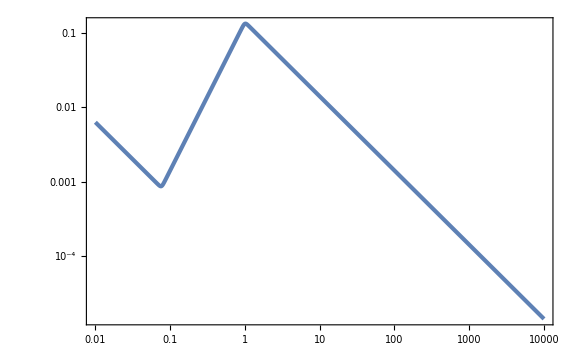

```mathematica
LogLogPlot[z[-x]/.{τs->-1,τ0->-10^4,lnDt->lndt,ϵ0->10^-2},{x,10^-2,10^4}]
```

```mathematica
EoM=vk''[τ]+(k^2-z''[τ]/z[τ])vk[τ]==0//Simplify
```

((-2^(3+80 lnDt) 5^(80 lnDt) τ^160+4^(1+40 lnDt) 5^(80 lnDt) k^2 τ^162+2^(1+40 lnDt) 5^(40 lnDt) (-137+121 10^(40 lnDt)) τ^120 τs^40+2^(3+40 lnDt) 5^(40 lnDt) (1+10^(40 lnDt)) k^2 τ^122 τs^40+(-35-7 2^(1+40 lnDt) 5^(40 lnDt)+10^(80 lnDt)) τ^80 τs^80+4 (1+4^(1+20 lnDt) 5^(40 lnDt)+10^(80 lnDt)) k^2 τ^82 τs^80-2 (-103+119 10^(40 lnDt)) τ^40 τs^120+8 (1+10^(40 lnDt)) k^2 τ^42 τs^120-8 τs^160+4 k^2 τ^2 τs^160+6 (-1+10^(40 lnDt)) τ^40 τs^40 (43 10^(40 lnDt) τ^80+6 τ^40 τs^40-37 τs^80) Coth[20 lnDt Log[10]]-9 (-1+10^(40 lnDt))^2 τ^80 τs^80 Coth[20 lnDt Log[10]]^2) vk[τ])/(4 τ^2 (τ^40+τs^40)^2 (10^(40 lnDt) τ^40+τs^40)^2)+vk''[τ]==0

```mathematica
kL=3 10^-3;
kS=10;
vkL[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τs->-1,τ0->-10^4,lnDt->lndt,k->kL},vk[τ],{τ,-10^4,-10^-2},WorkingPrecision->30][[1]];//AbsoluteTiming
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τs->-1,τ0->-10^2,lnDt->lndt,k->kS},vk[τ],{τ,-10^2,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];//AbsoluteTiming
```

{0.728218,Null}

{4.20463,Null}

```mathematica
ζkL[τ_]=vkL[τ]/z[τ]/.{τs->-1,τ0->-10^4,lnDt->lndt,ϵ0->10^-2};
ζkS[τ_]=vkS[τ]/z[τ]/.{τs->-1,τ0->-10^4,lnDt->lndt,ϵ0->10^-2};
PζkL[τ_]=Norm[ζkL[τ]]^2;
PζkS[τ_]=Norm[ζkS[τ]]^2;
```

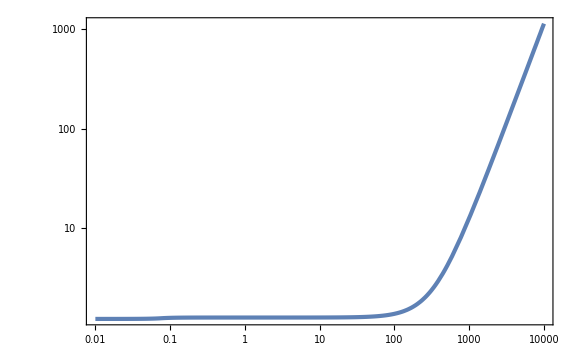

```mathematica
LogLogPlot[kL^3/(2 π^2)PζkL[-x],{x,10^4,10^-2},PlotRange->Full]
```

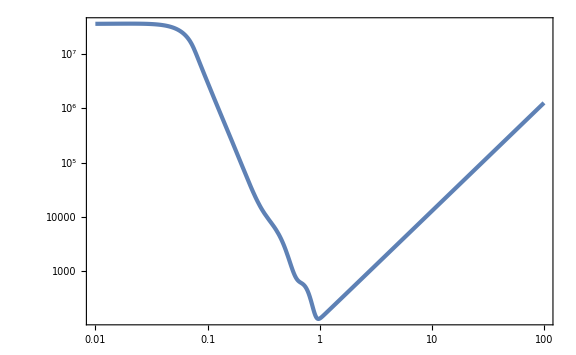

```mathematica
LogLogPlot[kS^3/(2 π^2)PζkS[-x],{x,10^2,10^-2}]
```

```mathematica
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
```

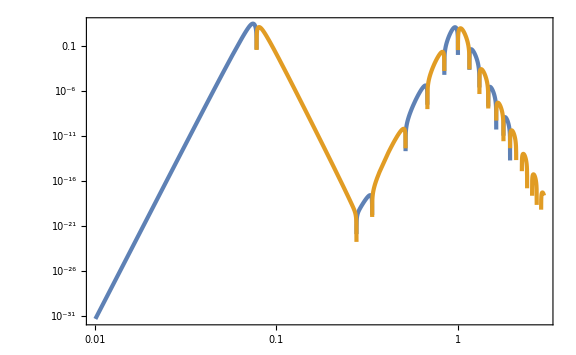

```mathematica
LogLogPlot[{5/3 1/(PζkL[-10^-2]PζkS[-10^-2])Im[1/τp^2(ϵ[-τp]η'[-τp]/.{τs->-1,τ0->-10^4,lnDt->lndt,ϵ0->10^-2})pktk[-10^-2,-τp]],-5/3 1/(PζkL[-10^-2]PζkS[-10^-2])1Im[1/τp^2(ϵ[-τp]η'[-τp]/.{τs->-1,τ0->-10^4,lnDt->lndt,ϵ0->10^-2})pktk[-10^-2,-τp]]},{τp,10^-2,3}]
```

```mathematica
5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[1/τp^2(ϵ[τp]η'[τp]/.{τs->-1,τ0->-10^4,lnDt->lndt,ϵ0->10^-2})pktk[-10^-2,τp]],{τp,-3,-10^-2}]
```

0.27083

```mathematica
Clear[kS,vkS,ζkS,PζkS,pktk];
fNLList=ParallelTable[{kS,
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τs->-1,τ0->-10^2,lnDt->lndt,k->kS},vk[τ],{τ,-10^2,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
ζkS[τ_]=vkS[τ]/z[τ]/.{τs->-1,τ0->-10^4,lnDt->lndt,ϵ0->10^-2};
PζkS[τ_]=Norm[ζkS[τ]]^2;
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[1/τp^2(ϵ[τp]η'[τp]/.{τs->-1,τ0->-10^4,lnDt->lndt,ϵ0->10^-2})pktk[-10^-2,τp]],{τp,-3,-10^-2}]},{kS,1,10,10^-2}];//AbsoluteTiming
```

{467.449,Null}

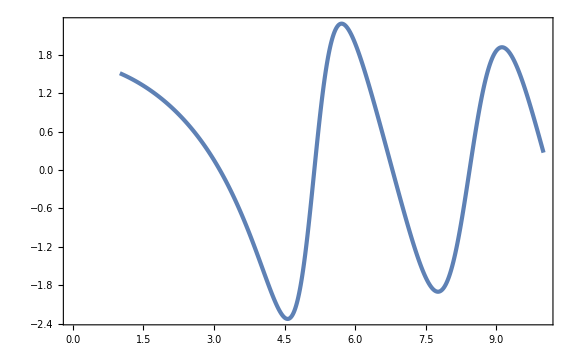

```mathematica
ListPlot[fNLList]
```